## For a general optimal control problem

### Need to minimize functional such as J = (∫_0)^T{L(x(t),u(t)) - λ(t) (dx/dt - f(x(t),u(t)) } dt where we assume that the Langrangian L and the cost function f do not depend explicitly on time nor on derivatives of x and u. Also, the final time T is fixed.

### The solution to this optimization, with these assumption, yields these 4 conditions: 1) H = L + λ f = constant, where H is the Hamiltonian, 2) dλ/dt=-((∂L)/(∂x)+λ (∂f)/(∂x)), 3) (∂L)/(∂u)+λ (∂f)/(∂u)=0, 4) dx/dt=f(x,u).

## Stefano’s equations (AWR 2013)

### No upper limit on g(t)

In the case of photosynthesis, the photosynthetic rate A(x(t),g(t)) needs to be maximized (replacing L(x(t),g(t)). It depends on the stomatal conductance g(t) and the soil moisture x(t). However, during drydown the cost function is the reduction of soil moisture with time dx/dt=f(g,x). Based on ecohydrological approaches, f = -(L + E)/(n Z_r) where L is the soil leakage term, E is the evapotranspiration term, n is the soil porosity, and Z_r is the rooting depth.
If g << g_a where g_a is the boundary-layer conductance, then E(t) = ν a g(t) D. The value ν is there to convert to the appropriate units, a = 1.6 is the ratio of water vapor to CO2 diffusivity, and D is the vapor pressure deficit of water. The leakage L is written as a power law of soil moisture L(t) = γ (x(t))^c
A = (g(t)c_a k)/(g(t) + k), where c_a is the atmospheric CO2 concentration and k is the carboxylation efficiency.

With these terms defined we can write the following conditions:
1) (g(t) c_a k)/(g(t) + k)-λ(t) (γ (x(t))^c+ν a g(t) D)/(n Z_r) = constant = H,
2) (dλ(t))/dt= - (0 +(λ(t) γ c (x(t))^(c-1))/(n Z_r))=-(λ(t) γ c (x(t))^(c-1))/(n Z_r),
3) (c_a k^2)/[g(t)+k]^2-(ν a D λ(t))/(n Z_r)=0,
4) (dx(t))/dt=-(γ (x(t))^c+ν a g(t) D)/(n Z_r).

```mathematica
Column[{
"Table of constants",
Grid[{
{"γ","α","β","ν"},
{Column[{"moisture power-law","L(t) = γ x(t)"},Center],"(ν a)/(n SubscriptBox[Z, r])","γ","(LAI SubscriptBox[M, w])/ρ_w"}
},Dividers->All]
},Center]
```

Table of constants
γ | α | β | ν
moisture power-law
L(t) = γ x(t) | (ν a)/(n SubscriptBox[Z, r]) | γ | (LAI SubscriptBox[M, w])/ρ_w

### No soil moisture limitation

```mathematica
Grid[{
{"x(t)","β=γ/(n SubscriptBox[Z, r])","c","λ(t)"},
{0, "≥0", 0,"λ_0"}
},Dividers->All]
```

x(t) | β=γ/(n SubscriptBox[Z, r]) | c | λ(t)
0 | ≥0 | 0 | λ_0

```mathematica
optg=Last[DSolve[(ca (k)^2)/(g[t]+k)^2-(ν a VPD λ)/(n Zr)==0,g[t] ,t ]]//Simplify
```

{g[t]→k (-1+(√ca √n √Zr)/(√a √VPD √λ √ν))}

```mathematica
optx=Collect[First[DSolve[{x'[t]==-(γ+ν a g[t]VPD)/(n Zr),x[0]==x0}/.optg,x[t],t]],t]
```

{x[t]→x0+(t (-γ √λ-√a √ca k √n √VPD √Zr √ν+a k VPD √λ ν))/(n Zr √λ)}

```mathematica
optLam=First[Solve[((x[t]/.optx)/.t->T)==0,λ]]
```

{λ→(a ca k^2 n T^2 VPD Zr ν)/(n x0 Zr-T γ+a k T VPD ν)^2}

An asymptote could exists as can be seen from the denominator of λ.

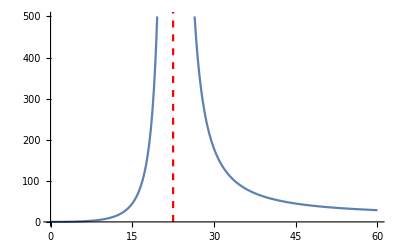

```mathematica
constants={T->Quantity[t,"Days"],γ->Quantity[0.01, ("Meters")/("Days")],VPD->Quantity[0.015, ("Moles")/("Moles")],k->Quantity[0.05, ("Moles")/(("Meters")^2 "Seconds")],x0->0.8,Zr->Quantity[0.3, "Meters"],ca->Quantity[350, ("Micromoles")/("Moles")],a->1.6,n->Quantity[0.5, ("Meters")^3/("Meters")^3],ν->(Quantity[5, ("Meters")^2/("Meters")^2]*Quantity[0.018, ("Kilograms")/("Moles")]*Quantity[12, ("Hours")/("Days")])/Quantity[1000, ("Kilograms")/("Meters")^3]};
lamSol=λ/.optLam/.constants;
asymptoteAbscissa=QuantityMagnitude[((-x0 n Zr)/(ν a k VPD - γ))/.constants];
Show[
Plot[UnitConvert[lamSol*(ν/(n Zr)/.constants),"Millimoles"/"Moles"]/.t->T,{T,0,60},PlotRange->{0,500}],
ListLinePlot[{{asymptoteAbscissa,0},{asymptoteAbscissa,10000}},PlotStyle->{Red,Dashed}]
]
```

```mathematica
x[t]/.optx/.constants/.λ->lamSol
```

0.8+t (-0.04 per day)

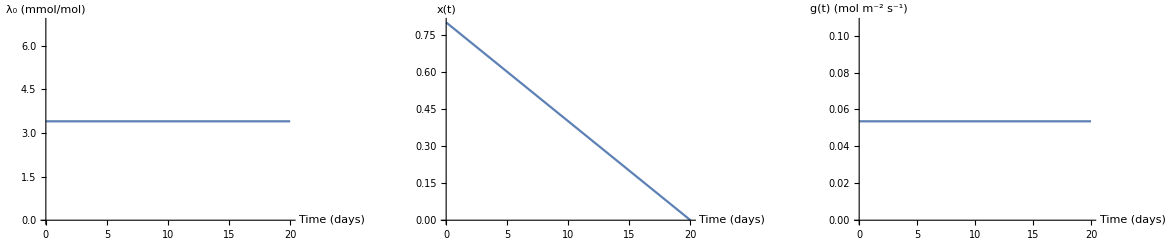

```mathematica
constants={T->Quantity[20, "Days"],γ->Quantity[0.001, ("Meters")/("Days")],VPD->Quantity[0.015, ("Moles")/("Moles")],k->Quantity[0.05, ("Moles")/(("Meters")^2 "Seconds")],x0->0.8,Zr->Quantity[0.3, "Meters"],ca->Quantity[350, ("Micromoles")/("Moles")],a->1.6,n->Quantity[0.5, ("Meters")^3/("Meters")^3],ν->(Quantity[5, ("Meters")^2/("Meters")^2]*Quantity[0.018, ("Kilograms")/("Moles")]*Quantity[12, ("Hours")/("Days")])/Quantity[1000, ("Kilograms")/("Meters")^3]};
lamSol=λ/.optLam/.constants;
lambdaPlot=Plot[UnitConvert[lamSol*(ν/(n Zr)/.constants),"Millimoles"/"Moles"],{T,0,20},
AxesLabel->{"Time (days)","λ_0 (mmol/mol)"},ImageSize->Medium];
xPlot=Plot[x[t]/.optx/.constants/.λ->lamSol/.t->Quantity[tvar,"Days"],{tvar,0,20},
AxesLabel->{"Time (days)","x(t)"}];
gPlot=Plot[g[t]/.optg/.constants/.λ->lamSol/.t->Quantity[tvar,"Days"],{tvar,0,20},
AxesLabel->{"Time (days)","g(t) ("<>"mol m^-2 s^-1"<>")"}];
GraphicsRow[{lambdaPlot,xPlot,gPlot}]
```

```mathematica
Clear[gplot]
```

### Leakage independent of soil moisture, no deep percolation, and no competing plants (c = 0 or γ = 0) → Loss function depends only on transpiration

From 2), (dλ(t))/dt= 0 → λ(t) = λ_0
Therefore, from 3), g_opt(t) = k [√(c_a/(α D λ_0))-1] , where α = ν a (n Z_r)^-1   .
And, from 4) x(t) = x_0 - (β + α g_opt(t) D)t, where β = γ/(n Z_r).

### If soil moisture places an upper bound on g(t): g_b(x)=k_SR/(ν a D)x_b(t) where k_SR is the linearity constant between E and x(t) such as E_SR[x(t)] = k_SR x(t)

In this equation I diverge from Stefano’s approach as I feel this is clearer. To constrain g(t)<g_b(x), we define a slack function that I call s(x,t) where g(t)-g_b(x)+s^2(x,g,t) = 0.
Now we need to maximize J = (∫_0)^T{A(x(t),g(t)) - λ(t) ×(dx/dt - f(x(t),g(t))  - μ(t)×(g(t)- g_b(t) + s(x(t),g(t),t)}  dt